```mathematica
Clear["`*"]
```

```mathematica
j=I;
```

```mathematica
A=Abs[(j 2 Pi f L)/(1-(2 Pi f)^2 L c)];
dBCuttoff= 1/10;
solve=Solve[A==dBCuttoff,{f}];
lowPole=f/.solve[[3]]
highPole=f/.solve[[4]]

Solve[A== dBCuttoff&& highPole-lowPole==10000,{L,c}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(-5 L+√(c L+25 L^2))/(2 c L π)

(5 L+√(c L+25 L^2))/(2 c L π)

{{L→500/((-10000+f) f π),c→1/(2000 π)},{L→500/(f (10000+f) π),c→1/(2000 π)}}

1/200 ⅇ^(-(ⅈ ω^2)/(20000 π)) (-ⅈ FresnelC[ω/(100 π)]-ⅈ FresnelC[100-ω/(100 π)]+FresnelS[ω/(100 π)]+FresnelS[100-ω/(100 π)]+ⅇ^((ⅈ ω^2)/(10000 π)) (-ⅈ FresnelC[ω/(100 π)]+ⅈ FresnelC[100+ω/(100 π)]-FresnelS[ω/(100 π)]+FresnelS[100+ω/(100 π)]))

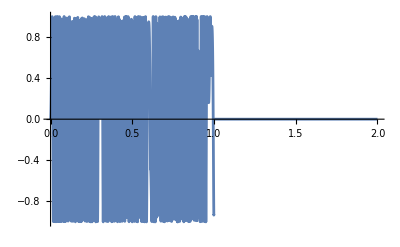

```mathematica
f0=0;
fmax=5000;
T=1;
k=(fmax-f0)/T;
V=Sin[2Pi(f0 t+k/2 t^2)](UnitStep[t]-UnitStep[t-T]);

Vω=FourierTransform[V,t,ω,FourierParameters->{1,-1}]

Plot[V,{t, 0, 2}]
```

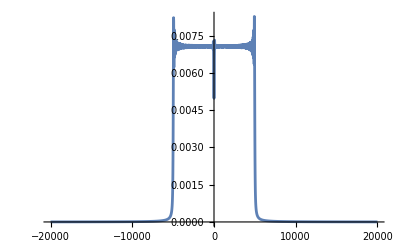

```mathematica
Plot[Abs[Vω]/.{ω-> 2 Pi f},{f, -20000, 20000}, PlotRange->All]
```